Patent Claims Analytics

Lee, Nae Eoun

Alessandrini, Giulio

Massachusetts Institute of Technology

Most representative image

-Graphics-

Abstract

GOAL OF THE PROJECT: Patent claims within a patent application or patent define the scope of the invention. In order to enforce the full scope of a patent, it is imperative for inventors, firms, and companies to make sure that the patent’s scope is not covered by prior publications and competitors’ patents (referred to as “prior art”) available in the public domain. For this reason, most companies with a patent portfolio spend a substantial amount of resources in searching for potentially troubling prior art. This project is a first step to optimize this process and offers an analytic tool to better categorize and analyze the relationship between patents by clustering them based on claim term frequency.

SUMMARY OF WORK: For the US patent grant full-text files from USPTO, the patent information including patent number, invention title, number of claims, and claim text was extracted using the headings of xml files, and WordCounts was executed on the invention title and claim text cleaned to obtain the three most frequently used words. Embeddings using NetModel called GloVe were used to turn those words into high-dimensional vector representations and group them together with semantically similar data in a vector space. Non-hierarchical clusterings using ClusterClassify were performed with various methods including Agglomerate, DBSCAN, GaussianMixture, and with specified number of clusters for KMean. It also demonstrated the prominent trends in patent grant in time-series by matching the USPTO’s classification system with NBER’s classification categories and analyzing the counts of patents in each category per yer. In addition, for analysis of each patent claim, Scope Checker was created to detect the most relevant and detailed information in patent’s description part for a given claim text by constructing a DistanceMatrix between the claim sentence and description sentences.

RESULTS AND FUTURE  WORK: The non-hierarchal clustering using 100-dimensional vector representations of each of three words created using GloVe produced very small numbers of clusters which were trivial while the K-means clustering with specified number of clusters could group the patents semantically pretty well. Then, classification using USPTO’s classification codes demonstrated that patent grants have been continuously increased, and especially, the number of patents related to computer and software field has been greatly increased. Lastly, the Scope Check successfully produced the relevant details of a given patent claim.The patent claim analytics need to be further improved by taking more frequently used words, taking phrases instead of words, or adding more neural network layers that can add distinguishable features. The clustering also can be improved by methods with optimized number of clusters that can minimize the dissimilarity within each cluster while maximizing it between different clusters or by taking account of classification system together.

Everything above this bar is your poster. Make sure it fits on a single page. "Preview Poster"

Additional concise content for 2 minute presentation

### Constructing an Analysis Matrix for Randomly Selected Patents

### Constructing Vector Representations of Words using NetModel, GloVe

```mathematica
net = NetModel["GloVe 100-Dimensional Word Vectors Trained on Wikipedia and Gigaword-5 Data"]
```

EmbeddingLayer[<>]

### Non-hierarchical clustering using ClusterClassify

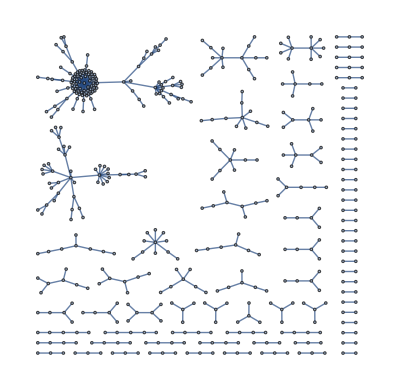

### Time Series Data

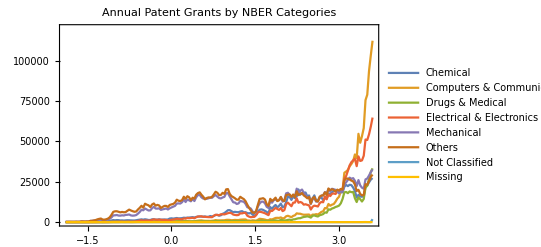

### Patent Scope Checker

Title: Method and system for presenting input expressions and evaluations of the input expressions on a workspace of a computational system
Claim: 2: The method according to claim 1, wherein the first user interface mechanism and the second user interface mechanism are different user interface mechanisms.
Description:{For example, the first GUI mechanism and the second GUI mechanism could be different states of a single GUI mechanism.,If a pull-down menu is utilized, the first GUI mechanism may be activated by selecting an appropriate item in the menu.,For instance, the second GUI mechanism may be presented in response to activation of the first GUI mechanism.}

{0,173,141,108,122,125,165,126,119,117,141,123,136,253,146,123,116,120,127,122,121,1528,212,119,120,203,221,180,153,112,192,227,185,109,203,172,135,117,245,214,179,129,118,136,115,177,128,213,261,124,121,129,126,114,119,123,118,119,173,118,116,120,148,121,116,126,243,122,163,132,157,125,153,129,165,122,119,120,123,137,119,122,111,122,145,119,121,116,244,117,131,128,118,117,144,125,126,119,116,120,301,127,112,123,133,119,192,117,122,127,116,130,135,121,117,142,134,126,119,196,123,121,117,168,120,112,135,123,123,117,117,123,117,115,116,111,147,122,133,190,266,118,150,123,142,116,104,121,120,122,128,147,108,118,127,126,147,122,113,128,157,118,112,147,135,115,106,147,116,108,193,251,124,152,121,140,116,107,121,120,119,132,132,113,116,132,130,121,124,126,112,134,158,147,111,118,139,91,352,222,180,198,123,226,120,119,144,116,127,120,116,118,118,124,139,122,160,116,111,121,133,119,193,115,121,133,119,191,121,122,127,116,120,127,115,127,116,121,117,119,135,121,119,194,123,118,119,135,121,119,192,127,308,120,125,154,117,114,128,128,122,118,119,120,115,136,151,173,125,201,119,120,116,118,183,112,171,148,156,139,139,126,153,216,265,285,120,142,159}

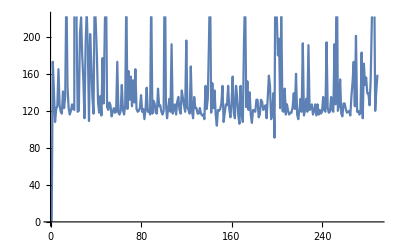

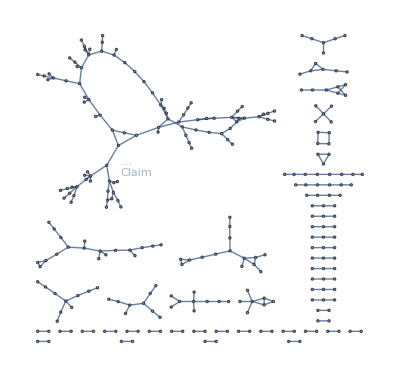

```mathematica
patentScopeChecker["ipg130326.xml","08407580",2]
```

Everything above this bar is in your 2 minute presentation. "Preview Presentation"

Detailed Records of the Project

Main Results in Detail

The randomly selected patents were parsed, extracted for their information including patent number, title, number of claims, and three most frequently used words, and saved in a dataset by finding text with corresponding headings of xml files.

```mathematica
patentAnalysisMatrix
```

Dataset[<>]

The vector representations of three most frequently used words in each patent were created using NetModel called GloVe.

```mathematica
net = NetModel["GloVe 100-Dimensional Word Vectors Trained on Wikipedia and Gigaword-5 Data"]
```

EmbeddingLayer[<>]

```mathematica
wordToVec = net /@Normal[patentAnalysisMatrix[All,"Words"]];
```

Non-hierarchal clustering with various methods without specifying the number of clusters resulted in only one or two clusters for >1000 patents, indicating that the distance between patents within a cluster would be large and the clustering method using the word vectors . Clustering for small data set, like 10 patents, often resulted in 7~8 clusters, showing that those patents were diverse in topic area or three words might not be enough to characterize a patent. However, the K-means clustering with specified number of clusters (chosen to be similar to the number of NBER categories) produced a classifier which could cluster the patents semantically well.
The NearestNeighborGraph to show the distances between most frequently used words had one or two large clusters which were consistent with the results from clustering using ClusterClassify. It was also consistent proportionally with the counts of patents categorized by classification.

```mathematica
NearestNeighborGraph[Values[wordToVec[[;;,1]]]]
```

-Graphics-

By counting the number of patent grant per yer, we demonstrated that the number of patent grants has been continuously increased, but the log-plot suggests that its growth rate has been roughly same over last thirty years. Time-series patent grant was also analyzed with data obtained by matching the USPTO’s classification code, if any in each patent, into one of six NBER’s categories.

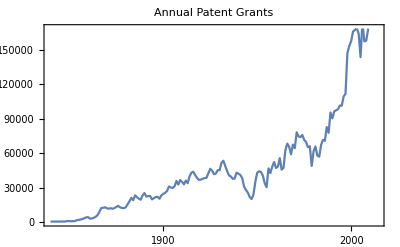
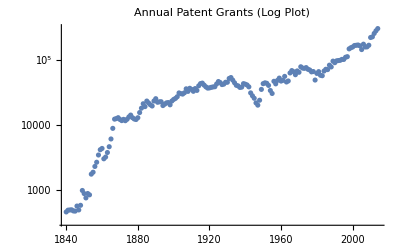

-Graphics-

Scope Checker, patentScopeChecker[file name, patent number, claim number], successfully detects the relevant details in the description/specification part of a patent document for a given claim text. These sentences corresponds to the three smallest values in the DistanceMatrix between the claim text and the description text, and NearestNeighborMatrix demonstrates how the claim text is related to the description text.

```mathematica
patentScopeChecker["ipg130326.xml","08407580",2]
```

Title: Method and system for presenting input expressions and evaluations of the input expressions on a workspace of a computational system
Claim: 2: The method according to claim 1, wherein the first user interface mechanism and the second user interface mechanism are different user interface mechanisms.
Description:{For example, the first GUI mechanism and the second GUI mechanism could be different states of a single GUI mechanism.,If a pull-down menu is utilized, the first GUI mechanism may be activated by selecting an appropriate item in the menu.,For instance, the second GUI mechanism may be presented in response to activation of the first GUI mechanism.}

{0,173,141,108,122,125,165,126,119,117,141,123,136,253,146,123,116,120,127,122,121,1528,212,119,120,203,221,180,153,112,192,227,185,109,203,172,135,117,245,214,179,129,118,136,115,177,128,213,261,124,121,129,126,114,119,123,118,119,173,118,116,120,148,121,116,126,243,122,163,132,157,125,153,129,165,122,119,120,123,137,119,122,111,122,145,119,121,116,244,117,131,128,118,117,144,125,126,119,116,120,301,127,112,123,133,119,192,117,122,127,116,130,135,121,117,142,134,126,119,196,123,121,117,168,120,112,135,123,123,117,117,123,117,115,116,111,147,122,133,190,266,118,150,123,142,116,104,121,120,122,128,147,108,118,127,126,147,122,113,128,157,118,112,147,135,115,106,147,116,108,193,251,124,152,121,140,116,107,121,120,119,132,132,113,116,132,130,121,124,126,112,134,158,147,111,118,139,91,352,222,180,198,123,226,120,119,144,116,127,120,116,118,118,124,139,122,160,116,111,121,133,119,193,115,121,133,119,191,121,122,127,116,120,127,115,127,116,121,117,119,135,121,119,194,123,118,119,135,121,119,192,127,308,120,125,154,117,114,128,128,122,118,119,120,115,136,151,173,125,201,119,120,116,118,183,112,171,148,156,139,139,126,153,216,265,285,120,142,159}

-Graphics-

-Graphics-

Code

GitHub: https://github.com/lne817/WSS-17/blob/master/Project/Project_code.nb

Written Content / Lesson Plans

Patents are classified by the USPTO into patent classes and subclasses based on the subject matter of the patent claims. Thus, we can use patent class/subclass information to group or cluster patents that have common claimed subject matter. Here, instead of the USTPO’s patent classification systems which have large numbers of categories and largely designed for administrative purposes, thus limiting their value for research purposes, the National Bureau of Economic Research (NBER) categories, which Hall, Jaffe, and Trajtenberg (2001) developed by aggregating USPC classes into six economically relevant technology categories (and 37 sub-categories) and classified granted patents accordingly, were applied to create the times series data.

Conclusions in Detail

While the US Patent Classification System reflects the Patent Examiner’s view of what he or she perceived as the main thrust of the patented invention, our natural language processing on patent claims using the claim term frequency was expected to reflect more the actual words used by the patent applicant in defining his or her invention. However, the non-hierarchal clustering using the vector representations of three most frequently used words created by GloVe resulted in one or two clusters which are trivial and not meaningful, but the K-means clustering with the number of clusters specified produced clusters within which the patents were semantically close to each other. The time-series data with counts of patent grant per category by USPOT’s classification re-categorized into NBER’s classification system implicates that those patents in Computers & Communication are more probable to be invalidated, and people need more than mere implementation to be patent eligible. Lastly, the Scope Checker was to construct the distance matrix between the claim sentence and the sentences in description/specification part of a patent, and find the most related text with the smallest distances. It was successful in detecting the text in the description part that was well relevant with and details a given claim text, and thus it is expected that it could help people clarify the scope and details of each claim.

All Visualizations

NearestNeighborGraph to show the distances between patents using three words’ vector:

```mathematica
clusterGraph = NearestNeighborGraph[Flatten /@Values[wordToVec]]
```

-Graphics3D-

Additional results from Scope Checker:

Title: Power converter
Claim: 4: The power converter of claim 1, wherein the air intake direction is substantially perpendicular to the air discharge direction.
Description:
{The direction opposite to the front direction will be defined as a rear direction.,The direction horizontally intersecting the front-rear direction will be defined as a left-right direction.,The direction vertically intersecting the front-rear direction will be defined as an up-down direction.}

{0,198,125,398,209,240,830,161,146,101,104,100,103,104,266,101,90,126,191,124,103,101,93,94,121,102,128,97,76,77,77,114,110,371,87,388,103,232,104,92,95,93,115,103,95,98,108,97,167,148,138,107,137,167,108,117,97,117,98,99,94,98,91,96,96,92,98,112,96,108,93,99,106,149,102,128,111,97,124,124,95,177,96,94,148,99,198,116,115,85,85,392,97,182,147,92,95,212,216,165,263,94,102,91,97,87,126,131,114,177,108,123,134,130,109,96,198,130,97,108,89,97,120,313,127,93,150,90,160,97,132,194,268,110,125,116,126,135,126,105,91,167,99,103,186,166,139,175,260,93,92,185,181,95,137,93,109,97,203,130}

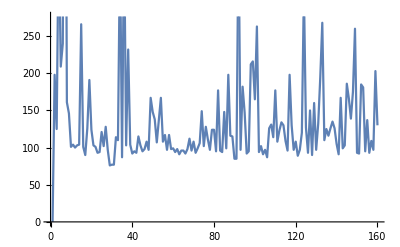

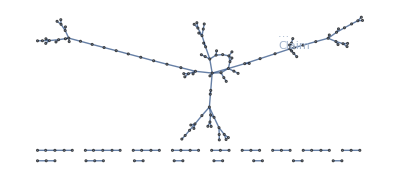

```mathematica
patentScopeChecker["ipg160105.xml","09232684",4]
```

Data Sources Links/References

USPTO Bulk Data Storage System: https://bulkdata.uspto.gov/
USPTO Historical Patent Data Files: https://www.uspto.gov/learning-and-resources/electronic-data-products/historical-patent-data-files
NBER Patent Data Project: https://sites.google.com/site/patentdataproject/
Hall, B. H., A. B. Jaffe, and M. Trajtenberg (2001). “The NBER Patent Citation Data File: Lessons, Insights and Methodological Tools.” NBER Working Paper 8498.

Future Directions

Compared to USPTO’s classification (which were reclassified into NBER’s classification system) made by human, our clustering methods using frequently used words would need further modification to clearly distinguish patents within a wide range of topic area and determine the scopes of their claims. I would suggest several methods that can further improve the patent claim analytics using Wolfram Language including:

Evaluating on more words.

Adding neural network layers to get the vectors weighted with each word frequency in text.

Constructing vectors for frequently used phrases instead of words.

Optimizing number of clusters to minimize dissimilarity within each cluster and maximize dissimilarity between clusters.

Classification system combined clustering methods.

Clustering within Utility patents (for inventions), which can be distinguished by patent numbers without prefix (####### for Utility, D###### for Design, PP###### for Plant) to improve clustering quality.

Background Info Links/References

Pennington, J., R. Socher, and C. D. Manning (2014). “GloVe: Global Vectors for Word Representation.”
Hall, B. H., A. B. Jaffe, and M. Trajtenberg (2001). “The NBER Patent Citation Data File: Lessons, Insights and Methodological Tools.” NBER Working Paper 8498.

Keywords

Provide keywords as items

Patent Analytics

Patent Clustering

Patent Classification

Patent Claim Scope

Other

Date

Last Modified: Wednesday, July 05, 2017

```mathematica
"Add Timestamp"
```